# Thermoelectrics vs Effective Mass (P+IP) w/ deformation-potential and polar-optical scattering w/ Brooks-Herring theory for ionized-impurity scattering

### Units, Conversions, and Constants

```mathematica
Clear[en,k,m,mu,kx,ky,kz];Needs["PlotLegends`"];Needs["FunctionApproximations`"]

h2ev=27.211;ev2j=1.602*10^-19;q=1.602*10^-19;mass=9.11*10^-31;bohr2m=5.29*10^-11;
au2sec=2.4188*10^-17;au2cond=(q/au2sec)^2/bohr2m^3*au2sec^3/mass;

gap=0/h2ev;kB=8.6173303*10^-5/h2ev;T=500;
ω=kB*T/2;kappalat=0.5/(h2ev*ev2j/bohr2m/au2sec);
```

### Band structure - Parabola+InvParabola

```mathematica
(* Lattice and BZ *)
bz=(1/15.)*2π/2;volume=bz^-3*(2π/2)^3/8;inflect=0.5*bz;
fix=1;

(* Effective Masses *)
mxc={0.05,0.15,0.5,1.5,5,15,50,150,500,  0.05,0.05,0.05,0.05,0.05, 0.05,0.05,0.05,0.05,0.05 };
myc={0.05,0.15,0.5,1.5,5,15,50,150,500,  0.05,0.05,0.05,0.05,0.05, 0.05,0.5,5,50,500};
mzc={0.05,0.15,0.5,1.5,5,15,50,150,500,  0.05,0.5,5,50,500, 0.05,0.5,5,50,500};
Nm=Length[mxc];
mdosc=(mxc*myc*mzc)^(1/3);mdosv=mdosc;

(* Fermi Level *)
Ef=Range[-0.2,0.2,0.01]/h2ev;
Nef=Length[Ef];
ef0=Position[Ef,0.]⟦1,1⟧;

(* Band Structure *)
Evpara=(-(kx^2/(2mx)+ky^2/(2my)+kz^2/(2mz))-gap/2)/.{mx->mxv,my->myv,mz->mzv};Ecpara=((kx^2/(2mx)+ky^2/(2my)+kz^2/(2mz))+gap/2)/.{mx->mxc,my->myc,mz->mzc};

slopex=D[Ecpara,kx]/.{kx->inflect,ky->0,kz->0};
slopey=D[Ecpara,ky]/.{ky->inflect,kx->0,kz->0};
slopez=D[Ecpara,kz]/.{kz->inflect,ky->0,kx->0};
mxcnew={};mycnew={};mzcnew={};
For[i=1,i≤Length[slopex],i++,
AppendTo[mxcnew,Solve[(bz-inflect)==x*slopex⟦i⟧]⟦All,1,2⟧⟦1⟧];
AppendTo[mycnew,Solve[(bz-inflect)==y*slopey⟦i⟧]⟦All,1,2⟧⟦1⟧];AppendTo[mzcnew,Solve[(bz-inflect)==z*slopez⟦i⟧]⟦All,1,2⟧⟦1⟧];
]

width[kx_,ky_,kz_]:=Module[{width},
If [inflect≥0.5*bz,
width=gap/2+((Min[Norm[kx],inflect])^2/(2mxc)+(inflect^2-(bz-Max[Norm[kx],inflect])^2)/(2mxcnew))+((Min[Norm[ky],inflect])^2/(2myc)+(inflect^2-(bz-Max[Norm[ky],inflect])^2)/(2mycnew))+((Min[Norm[kz],inflect])^2/(2mzc)+(inflect^2-(bz-Max[Norm[kz],inflect])^2)/(2mzcnew))-(Norm[(inflect^2-(bz-inflect)^2)]/2(1/mxcnew+1/mycnew+1/mzcnew)),
width=gap/2+((Min[Norm[kx],inflect])^2/(2mxc)+(inflect^2-(bz-Max[Norm[kx],inflect])^2)/(2mxcnew))+((Min[Norm[ky],inflect])^2/(2myc)+(inflect^2-(bz-Max[Norm[ky],inflect])^2)/(2mycnew))+((Min[Norm[kz],inflect])^2/(2mzc)+(inflect^2-(bz-Max[Norm[kz],inflect])^2)/(2mzcnew))+(Norm[(inflect^2-(bz-inflect)^2)]/2(1/mxcnew+1/mycnew+1/mzcnew))
];
Return[width]
]
Ec=width[kx,ky,kz];Ev=-width[kx,ky,kz];

Eint=3/4*kB*T*Log[mdosv⟦1⟧/mdosc⟦1⟧];
Ec=Ec-Eint;
Vc=Transpose[{D[Ec,kx],D[Ec,ky],D[Ec,kz]}]/.{Norm'[kx]->D[Sqrt[kx^2],kx],Norm'[ky]->D[Sqrt[ky^2],ky],Norm'[kz]->D[Sqrt[kz^2],kz]};

id=1;
Plot3D[Ec⟦id⟧/.kz->0,{kx,-bz,bz},{ky,-bz,bz},BoxRatios->{1,1,2},BoxStyle->Directive[Black,Thick,25],Ticks->None,AxesLabel->{"k_x","k_y",Rotate["Energy",π/2]},LabelStyle->{30},PlotRange->{Automatic,Automatic,{0,0.45}},PlotStyle->Directive[Cyan]]
```

-Graphics3D-

### BZ Discretization (Tetrahedron Integration)

```mathematica
meshtetra=26;Nktetra=meshtetra^3;
kpooltetra=Range[0,bz,bz/(meshtetra-1)]; (* Uniform Mesh *)
kpooltetra=(1-Cos[Range[0,π,π/(meshtetra-1)]])*bz/2; (* Cosine Mesh *)
klisttetra=ConstantArray[0,Nktetra];ijkindex=ConstantArray[0,Nktetra];
knodetetra=ConstantArray[0,meshtetra+1];knodetetra⟦1⟧=0;knodetetra⟦-1⟧=bz;
(* mid-points between k-points along a direction *)
Do[knodetetra⟦i+1⟧=Mean[{kpooltetra⟦i⟧,kpooltetra⟦i+1⟧}],{i,meshtetra-1}] 

Do[Do[Do[
ind=meshtetra^2*(i-1)+meshtetra*(j-1)+k;(* counter *)
klisttetra⟦ind⟧={kpooltetra⟦i⟧,kpooltetra⟦j⟧,kpooltetra⟦k⟧};
ijkindex⟦ind⟧={i,j,k};
,{k,meshtetra}],{j,meshtetra}],{i,meshtetra}]//AbsoluteTiming
klisttetra=Transpose[klisttetra];

Eclisttetra=ConstantArray[0,{Nm,Nktetra}];
Do[
Eclisttetra⟦All,i⟧=Ec/.{kx->klisttetra⟦1,i⟧,ky->klisttetra⟦2,i⟧,kz->klisttetra⟦3,i⟧};
,{i,Nktetra}]//AbsoluteTiming
```

{0.070271,Null}

{8.94734,Null}

### BZ Discretization (Dense)

```mathematica
mesh=40;Nk=mesh^3;
kpool=Range[0,bz,bz/(mesh-1)];(* Uniform Mesh *)
(*kpool=Range[0,Sqrt[bz],Sqrt[bz]/(mesh-1)]^2;*) (* Sqrt Mesh *)
kpool=(-Cos[Range[0,π,π/(mesh-1)]]+1)*bz/2; (* Cosine Mesh *)

klist=ConstantArray[0,Nk];ijk=ConstantArray[0,Nk];wk=ConstantArray[0,Nk];
knode=ConstantArray[0,mesh+1];knode⟦1⟧=0;knode⟦-1⟧=bz;
(* mid-points between k-points along a direction *)
Do[knode⟦i+1⟧=Mean[{kpool⟦i⟧,kpool⟦i+1⟧}],{i,mesh-1}] 

Do[Do[Do[
ind=mesh^2*(i-1)+mesh*(j-1)+k; (* counter *)
klist⟦ind⟧={kpool⟦i⟧,kpool⟦j⟧,kpool⟦k⟧};
ijk⟦ind⟧={i,j,k};
wk⟦ind⟧=(knode⟦i+1⟧-knode⟦i⟧)*(knode⟦j+1⟧-knode⟦j⟧)*(knode⟦k+1⟧-knode⟦k⟧); (* box size as weights *)
,{k,mesh}],{j,mesh}],{i,mesh}]//AbsoluteTiming
klist=Transpose[klist];wk=wk/bz^3;
Print["Sanity Check: the weights sum up to ",Total[wk]]
```

{0.536195,Null}

Sanity Check: the weights sum up to 1.

### Band Structure Information

```mathematica
knorm=ConstantArray[0,Nk];velnorm=ConstantArray[0,{Nm,Nk}];mvel2=ConstantArray[0,{Nm,Nk}];
Eclist=ConstantArray[0,{Nm,Nk}];Vc2list=ConstantArray[0,{Nm,3,Nk}];

Do[
knorm⟦i⟧=10^-10+Norm[{kx,ky,kz}]/.{kx->klist⟦1,i⟧,ky->klist⟦2,i⟧,kz->klist⟦3,i⟧};
Eclist⟦All,i⟧=Ec/.{kx->klist⟦1,i⟧,ky->klist⟦2,i⟧,kz->klist⟦3,i⟧};
Vc2list⟦All,All,i⟧=Vc^2/.{kx->(klist⟦1,i⟧+10^-10),ky->(klist⟦2,i⟧+10^-10),kz->(klist⟦3,i⟧+10^-10)};
Do[
velnorm⟦m,i⟧=Sqrt[Total[Vc2list⟦m,All,i⟧]];
mvel2⟦m,i⟧=Vc2list⟦m,All,i⟧.{mxc⟦m⟧,myc⟦m⟧,mzc⟦m⟧};
,{m,Nm}];
,{i,Nk}]//AbsoluteTiming

f=1/(1+Exp[(en-mu)/kB/T]);df=D[f,en];
flistc=f/.en->Eclist;dflistc=df/.en->Eclist;
Now
```

{148.727,Null}

Sat 10 Oct 2020 00:21:34GMT-5.

#### Visualize weights

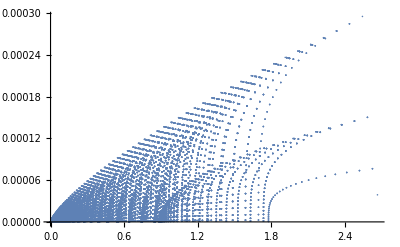

```mathematica
id=1;
ListPlot[Transpose[{Eclist⟦id⟧,wk}]*h2ev,PlotRange->Full]
```

### Tetrahedron DOS

This approach uses the coarser tetrahedra mesh. Skip if DOS is to be calculated using the Green's function approach.

```mathematica
If[Length[Kernels[]]≠$ProcessorCount,
CloseKernels[];LaunchKernels[]
]

Ntetra=6(meshtetra-1)^3;tetra=ConstantArray[0,Ntetra];wtetra=ConstantArray[0,Ntetra];
SetSharedVariable[tetra,wtetra];

(* Find all cubes and tetrahedra defined by the BZ mesh and their weights - tetra and dense meshes *)

ParallelDo[Do[Do[
ind=(meshtetra-1)^2*(i-1)+(meshtetra-1)*(j-1)+k;
ind1=Position[ijkindex,{i,j,k}]⟦1,1⟧;
ind2=Position[ijkindex,{i+1,j,k}]⟦1,1⟧;
ind3=Position[ijkindex,{i,j+1,k}]⟦1,1⟧;
ind4=Position[ijkindex,{i+1,j+1,k}]⟦1,1⟧;
ind5=Position[ijkindex,{i,j,k+1}]⟦1,1⟧;
ind6=Position[ijkindex,{i+1,j,k+1}]⟦1,1⟧;
ind7=Position[ijkindex,{i,j+1,k+1}]⟦1,1⟧;
ind8=Position[ijkindex,{i+1,j+1,k+1}]⟦1,1⟧;
cube={ind1,ind2,ind3,ind4,ind5,ind6,ind7,ind8};
volcube=Dot[klisttetra⟦All,ind5⟧-klisttetra⟦All,ind1⟧,Cross[klisttetra⟦All,ind2⟧-klisttetra⟦All,ind1⟧,klisttetra⟦All,ind3⟧-klisttetra⟦All,ind1⟧]];
(* Main diagonal is between verticies of index 3 and 6 *)
tetra⟦Range[6(ind-1)+1,6ind]⟧={{cube⟦1⟧,cube⟦2⟧,cube⟦3⟧,cube⟦6⟧},{cube⟦1⟧,cube⟦3⟧,cube⟦5⟧,cube⟦6⟧},{cube⟦3⟧,cube⟦5⟧,cube⟦6⟧,cube⟦7⟧},{cube⟦3⟧,cube⟦6⟧,cube⟦7⟧,cube⟦8⟧},{cube⟦3⟧,cube⟦4⟧,cube⟦6⟧,cube⟦8⟧},{cube⟦2⟧,cube⟦3⟧,cube⟦4⟧,cube⟦6⟧}};
wtetra⟦Range[6(ind-1)+1,6ind]⟧=volcube;

,{k,meshtetra-1}],{j,meshtetra-1}],{i,meshtetra-1}]//AbsoluteTiming
wtetra=wtetra/6/bz^3;

Print["Sanity Check: the tetra weights sum up to ",Total[wtetra]]

(* Function for tetrahedron integration of DOS *)
TetraDOS[energy_,id_]:=Module[{dosgrid,enlist,,enp,e21,e31,e41,e32,e42,e43,case},
enlist=Eclisttetra;
dosgrid=ConstantArray[0,Ntetra];
Do[
enp=Sort[{enlist⟦id,tetra⟦t,1⟧⟧,enlist⟦id,tetra⟦t,2⟧⟧,enlist⟦id,tetra⟦t,3⟧⟧,enlist⟦id,tetra⟦t,4⟧⟧}];
e21=enp⟦2⟧-enp⟦1⟧;e31=enp⟦3⟧-enp⟦1⟧;e41=enp⟦4⟧-enp⟦1⟧;
e32=enp⟦3⟧-enp⟦2⟧;e42=enp⟦4⟧-enp⟦2⟧;e43=enp⟦4⟧-enp⟦3⟧;
case=0;
If[energy>enp⟦1⟧&&energy<enp⟦2⟧,case=1;dosgrid⟦t⟧=wtetra⟦t⟧(3(energy-enp⟦1⟧)^2)/(e21*e31*e41)];
If[energy>enp⟦2⟧&&energy<enp⟦3⟧,case=2;dosgrid⟦t⟧=wtetra⟦t⟧1/(e31*e41)*(3e21+6(energy-enp⟦2⟧)-3((e31+e42)(energy-enp⟦2⟧)^2)/(e32*e42))];
If[energy>enp⟦3⟧&&energy<enp⟦4⟧,case=3;dosgrid⟦t⟧=wtetra⟦t⟧(3(enp⟦4⟧-energy)^2)/(e43*e42*e41)];
If[case==0,dosgrid⟦t⟧=10^-10]
,{t,Ntetra}];
Return[Total[dosgrid]]
]

Now
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

{212.88,Null}

Sanity Check: the tetra weights sum up to 1.

Sat 10 Oct 2020 00:25:09GMT-5.

```mathematica
(* Tag to control whether to recalculate tetrahedra DOS fit (1 = True) *)
REDOTETRA=1;

dos3dpara=(Sqrt[2] mdos^(3/2))/π^2 en^(1/2);
dosk=ConstantArray[0,{Nm,Nk}];dosωk=ConstantArray[0,{Nm,Nk}];dosatω=ConstantArray[0,Nm];
If[ValueQ[dosfit]==False,
dosfit=ConstantArray[0,Nm]
]
```

```mathematica
Do[(* Rather than computing DOS directly on the k-mesh, use a tetrar energy-mesh and then interpolate  *)
If[mdosc⟦m⟧≤0.15,
enmesh=Range[0,Max[Eclist⟦m⟧],Max[Eclist⟦m⟧]/5000], (* denser energy-mesh for dispersive bands *)
enmesh=Range[0,Max[Eclist⟦m⟧],Max[Eclist⟦m⟧]/500]
];
PrependTo[enmesh,Range[-10ω,-ω,ω]];(* Need some zero DOS points before and after *)
AppendTo[enmesh,Range[Max[Eclist⟦m⟧]+ω,Max[Eclist⟦m⟧]+10ω,ω]]; 
enmesh=Flatten[enmesh];
If[REDOTETRA==1,
If[MemberQ[{10,15},m]==False,
dos=TetraDOS[#,m]&/@enmesh;
dosfit⟦m⟧=Interpolation[Transpose[{enmesh,dos}],InterpolationOrder->1],
dosfit⟦m⟧=dosfit⟦1⟧;
];
];
dosk⟦m⟧=dosfit⟦m⟧/@Eclist⟦m⟧;
dosωk⟦m⟧=dosfit⟦m⟧/@(Eclist⟦m⟧-ω);
dosatω⟦m⟧=dosfit⟦m⟧[ω];
Print[m,Now];
,{m,Nm}]//AbsoluteTiming

(* This is normalizer w/r/t parabolic DOS whose reference volume is an arbitrary k-sphere. *)
enparamax=Min[Ec⟦1⟧/.{kx->inflect,ky->0,kz->0},Ec⟦1⟧/.{kx->0,ky->inflect,kz->0},Ec⟦1⟧/.{kx->0,ky->0,kz->inflect}];
dosnorm=NIntegrateInterpolatingFunction[dosfit⟦1⟧[en],{en,0,enparamax}]/NIntegrate[dos3dpara/.mdos->mdosc⟦1⟧,{en,0,enparamax}];
dos3dpara=dosnorm*dos3dpara;
```

1Sat 10 Oct 2020 02:26:26GMT-5.

2Sat 10 Oct 2020 04:19:29GMT-5.

3Sat 10 Oct 2020 04:31:28GMT-5.

4Sat 10 Oct 2020 04:43:08GMT-5.

5Sat 10 Oct 2020 04:55:06GMT-5.

6Sat 10 Oct 2020 05:06:46GMT-5.

7Sat 10 Oct 2020 05:18:47GMT-5.

8Sat 10 Oct 2020 05:30:27GMT-5.

9Sat 10 Oct 2020 05:42:26GMT-5.

10Sat 10 Oct 2020 05:42:26GMT-5.

11Sat 10 Oct 2020 07:35:53GMT-5.

12Sat 10 Oct 2020 07:47:34GMT-5.

13Sat 10 Oct 2020 07:59:15GMT-5.

14Sat 10 Oct 2020 08:10:55GMT-5.

15Sat 10 Oct 2020 08:10:56GMT-5.

16Sat 10 Oct 2020 08:22:35GMT-5.

17Sat 10 Oct 2020 08:34:18GMT-5.

18Sat 10 Oct 2020 08:46:01GMT-5.

19Sat 10 Oct 2020 08:57:44GMT-5.

{30162.9,Null}

### Green's Function DOS

This approach uses the dense mesh only. It is faster than tetrahedron integration but memory intensive in its current form.
This approach is less accurate near the band edges than the tetrahedron method and introduces more oscillations.
Skip if DOS is to be calculated by tetrahedron integration.

```mathematica
broad=8*10^-4;
G=1/(en-Eclist+I*broad);
dos3dpara=(Sqrt[2] mdos^(3/2))/π^2 en^(1/2);

dos=ConstantArray[0,Nm];dosk=ConstantArray[0,{Nm,Nk}];dosωk=ConstantArray[0,{Nm,Nk}];
dosatω=ConstantArray[0,Nm];

Do[
dos⟦m⟧=-Im[Total[G⟦m⟧*wk]];
dos⟦m⟧=dos⟦m⟧/NIntegrate[dos⟦m⟧,{en,0,Max[Eclist⟦m⟧]}];
dosk⟦m⟧=dos⟦m⟧/.en->Eclist⟦m⟧;
dosωk⟦m⟧=(dos⟦m⟧/.en->(enn-ω))/.enn->Eclist⟦m⟧;
dosatω⟦m⟧=dos⟦m⟧/.en->ω;
Print[m]
,{m,{1,2,10,11,15}}]//AbsoluteTiming

enparamax=Min[Ec⟦1⟧/.{kx->inflect,ky->0,kz->0},Ec⟦m⟧/.{kx->0,ky->inflect,kz->0},Ec⟦m⟧/.{kx->0,ky->0,kz->inflect}];
(* This is normalizer w/r/t parabolic DOS whose reference volume is an arbitrary k-sphere. *)
dosnorm=NIntegrate[dos⟦1⟧,{en,0,enparamax}]/NIntegrate[dos3dpara/.mdos->mdosc⟦1⟧,{en,0,enparamax}];
dos3dpara=dosnorm*dos3dpara;

Now
```

### Carrier Concentration

```mathematica
populationc=ConstantArray[0,{Nm,Nef}];
Do[Do[
finc=flistc⟦m⟧/.mu->Ef⟦ef⟧;
populationc⟦m,ef⟧=Total[finc*wk]/volume;
,{ef,Nef}],{m,Nm}]//AbsoluteTiming

Now
```

{215.61,Null}

Sat 10 Oct 2020 13:54:47GMT-5.

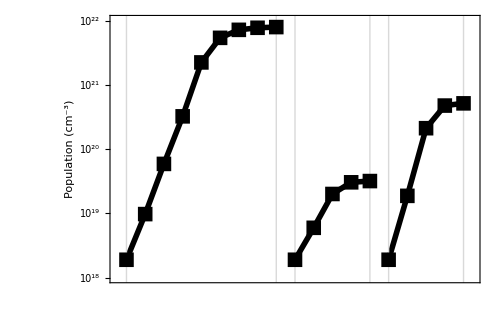

```mathematica
populationc=populationc/(bohr2m^3*10^6);
ListLogPlot[{populationc⟦Range[9],ef0⟧,Table[{i,populationc⟦i,ef0⟧},{i,10,14}],Table[{i,populationc⟦i,ef0⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]}},PlotMarkers->{{■,15}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,15,25}],None},{None,None}},FrameStyle->Directive[25,Black,Thick],Frame->True,FrameLabel->{None,"Population (cm^-3)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^18,10^22}},GridLines->{{1,9,10,14,15,19},None},GridLinesStyle->Thickness[0.002],ImageSize->500]
populationc=populationc*(bohr2m^3*10^6);
```

### Lifetimes

```mathematica
(* Parameters *)
Δ=0.4;Z=1;eps=30;epsinf=25;vs=4000/(bohr2m/au2sec);ρ=5000/(mass/bohr2m^3);
β=(nr*fratio)/(kB*T*eps);b=(4 mom^2)/β;dopec=1/Z populationc;
fermifunction=1/Gamma[z+1]*NIntegrate[y^z/(1+Exp[y-mu]),{y,0,∞}];
fermiratioc=(fermifunction/.{z->-0.5,mu->Ef/kB/T})/(fermifunction/.{z->0.5,mu->Ef/kB/T});

(* Deformation-Potential Scattering *)
taudef=FullSimplify[(π*ρ*vs^2 en^(-1/2))/(Sqrt[2] mdos^(3/2)kB*T*(Δ+mv2)^2)*dos3dpara/dosnew,Assumptions->{en>0,mdos>0}];

(* Polar-Optical Scattering *)
taupol=FullSimplify[en^(1/2)/(Sqrt[2]ω*mdos^(1/2))(1/epsinf-1/eps)^-1*mom/(2*en*mdos)^(1/2)*(mdos/mom)*vel(1/(Exp[ω/(kB*T)]-1)(Exp[ω/(kB*T)]*ArcSinh[dosnew1/dosω*HeavisideTheta[en-ω]]+ArcSinh[dosnew2/dosω]))^-1,Assumptions->{en>0,mdos>0}];

(* Ionized-Impurity Scattering *)
tauii=FullSimplify[(Sqrt[2]*mdos^(1/2)*eps^2*en^(3/2))/(π*dope*Z^2)*mom^4/(2*en*mdos)^2*dos3dpara/dosnew*(Log[1+b]-b/(1+b))^-1,Assumptions->{en>0,mdos>0}];

taudefc=ConstantArray[0,{Nm,Nef,Nk}];taupolc=ConstantArray[0,{Nm,Nef,Nk}];
tauiic=ConstantArray[0,{Nm,Nef,Nk}];tauc=ConstantArray[0,{Nm,Nef,Nk}];

Print["Computing Lifetimes..."]
Do[
(* Deformation-Potential Scattering *)
taudefc⟦m,1⟧=taudef/.{mv2->mvel2⟦m⟧,dosnew->dosk⟦m⟧};
Do[taudefc⟦m,ef⟧=taudefc⟦m,1⟧,{ef,2,Nef}];

(* Polar-Optical Scattering *)
taupolc⟦m,1⟧=taupol/.dosω->dosatω⟦m⟧/.{dosnew1->dosωk⟦m⟧,dosnew2->dosk⟦m⟧,vel->velnorm⟦m⟧,en->Eclist⟦m⟧};
Do[taupolc⟦m,ef⟧=taupolc⟦m,1⟧,{ef,2,Nef}];

(* Ionized-Impurity Scattering *)
Do[tauiic⟦m,ef⟧=tauii/.{nr->populationc⟦m,ef⟧,dope->dopec⟦m,ef⟧,fratio->fermiratioc⟦ef⟧}/.{dosnew->dosk⟦m⟧,mom->knorm,en->Eclist⟦m⟧};
,{ef,Nef}]

,{m,Nm}]//AbsoluteTiming

tauc=1/(1/tauiic+1/taudefc+1/taupolc);

Now
```

NIntegrate::inumr: The integrand y^z/(1+ⅇ^(-mu+y)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

Computing Lifetimes...

{13.5379,Null}

Sat 10 Oct 2020 13:55:05GMT-5.

### Calculate Boltzmann Integral - Conductivity

```mathematica
sigmac=ConstantArray[0,{Nm,Nef,3}];  sigmapolc=sigmac; sigmadefc=sigmac; sigmaiic=sigmac;
Do[Do[Do[

dfinc=-dflistc⟦m⟧/.mu->Ef⟦ef⟧;
v2dfc=Vc2list⟦m,j⟧*dfinc;

sigmadefc⟦m,ef,j⟧=Total[taudefc⟦m,ef⟧*v2dfc*wk]/volume;
sigmapolc⟦m,ef,j⟧=Total[taupolc⟦m,ef⟧*v2dfc*wk]/volume;
sigmaiic⟦m,ef,j⟧=Total[tauiic⟦m,ef⟧*v2dfc*wk]/volume;
sigmac⟦m,ef,j⟧=Total[tauc⟦m,ef⟧*v2dfc*wk]/volume;

,{j,3}],{ef,Nef}];

,{m,Nm}]//AbsoluteTiming
```

{1809.74,Null}

```mathematica
(* Polycrystalline properties via harmonic averaging *)
sigmadefcpoly=ConstantArray[0,{Nm,Nef}];sigmapolcpoly=ConstantArray[0,{Nm,Nef}];sigmaiicpoly=ConstantArray[0,{Nm,Nef}];
sigmacpoly=ConstantArray[0,{Nm,Nef}];
Do[
sigmadefcpoly⟦m⟧=HarmonicMean[Transpose[sigmadefc⟦m⟧]];
sigmapolcpoly⟦m⟧=HarmonicMean[Transpose[sigmapolc⟦m⟧]];
sigmaiicpoly⟦m⟧=HarmonicMean[Transpose[sigmaiic⟦m⟧]];
sigmacpoly⟦m⟧=HarmonicMean[Transpose[sigmac⟦m⟧]];
,{m,Nm}]
```

### Calculate Boltzmann Integrals - Thermoelectricity

```mathematica
zetac=ConstantArray[0,{Nm,Nef,3}];zetadefc=zetac;zetapolc=zetac;zetaiic=zetac;
Do[Do[Do[

Ecdiff=Ef⟦ef⟧-Eclist⟦m⟧;
dfinc=-dflistc⟦m⟧/.mu->Ef⟦ef⟧;
v2dfc=Vc2list⟦m,j⟧*dfinc;

zetadefc⟦m,ef,j⟧=Total[taudefc⟦m,ef⟧*Ecdiff*v2dfc*wk]/volume/T;
zetapolc⟦m,ef,j⟧=Total[taupolc⟦m,ef⟧*Ecdiff*v2dfc*wk]/volume/T;
zetaiic⟦m,ef,j⟧=Total[tauiic⟦m,ef⟧*Ecdiff*v2dfc*wk]/volume/T;
zetac⟦m,ef,j⟧=Total[tauc⟦m,ef⟧*Ecdiff*v2dfc*wk]/volume/T;

,{j,3}],{ef,Nef}],{m,Nm}]//AbsoluteTiming

Now
```

{1687.09,Null}

Sat 10 Oct 2020 14:53:22GMT-5.

```mathematica
zetadefcpoly=ConstantArray[0,{Nm,Nef}];zetapolcpoly=ConstantArray[0,{Nm,Nef}];zetaiicpoly=ConstantArray[0,{Nm,Nef}];
zetacpoly=ConstantArray[0,{Nm,Nef}];

(* Polycrystalline properties by harmonic averaging *)
Do[
zetadefcpoly⟦m⟧=HarmonicMean[Transpose[zetadefc⟦m⟧]];
zetapolcpoly⟦m⟧=HarmonicMean[Transpose[zetapolc⟦m⟧]];
zetaiicpoly⟦m⟧=HarmonicMean[Transpose[zetaiic⟦m⟧]];
zetacpoly⟦m⟧=HarmonicMean[Transpose[zetac⟦m⟧]];
,{m,Nm}]
```

### Calculate Boltzmann Integral - Carrier Thermal Conductivity

```mathematica
kappac=ConstantArray[0,{Nm,Nef,3}];kappadefc=kappac;kappapolc=kappac;kappaiic=kappac;
Do[Do[Do[

Ecdiff=Ef⟦ef⟧-Eclist⟦m⟧;
dfinc=-dflistc⟦m⟧/.mu->Ef⟦ef⟧;
v2dfc=Vc2list⟦m,j⟧*dfinc;

kappadefc⟦m,ef,j⟧=Total[taudefc⟦m,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;
kappapolc⟦m,ef,j⟧=Total[taupolc⟦m,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;
kappaiic⟦m,ef,j⟧=Total[tauiic⟦m,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;
kappac⟦m,ef,j⟧=Total[tauc⟦m,ef⟧*Ecdiff^2*v2dfc*wk]/volume/T;

,{j,3}],{ef,Nef}];

,{m,Nm}]//AbsoluteTiming

Now

kappac=(kappac)-zetac^2/sigmac*T;
kappadefc=(kappadefc)-zetadefc^2/sigmadefc*T;
kappapolc=(kappapolc)-zetapolc^2/sigmapolc*T;
kappaiic=(kappaiic)-zetaiic^2/sigmaiic*T;
```

{1681.31,Null}

Sat 10 Oct 2020 15:21:24GMT-5.

```mathematica
kappadefcpoly=ConstantArray[0,{Nm,Nef}];kappapolcpoly=ConstantArray[0,{Nm,Nef}];kappaiicpoly=ConstantArray[0,{Nm,Nef}];
kappacpoly=ConstantArray[0,{Nm,Nef}];

(* Polycrystalline properties via harmonic averaging *)
Do[
kappadefcpoly⟦m⟧=HarmonicMean[Transpose[kappadefc⟦m⟧]];
kappapolcpoly⟦m⟧=HarmonicMean[Transpose[kappapolc⟦m⟧]];
kappaiicpoly⟦m⟧=HarmonicMean[Transpose[kappaiic⟦m⟧]];
kappacpoly⟦m⟧=HarmonicMean[Transpose[kappac⟦m⟧]];
,{m,Nm}]
```

### Find Optimum E_F for PF or zT

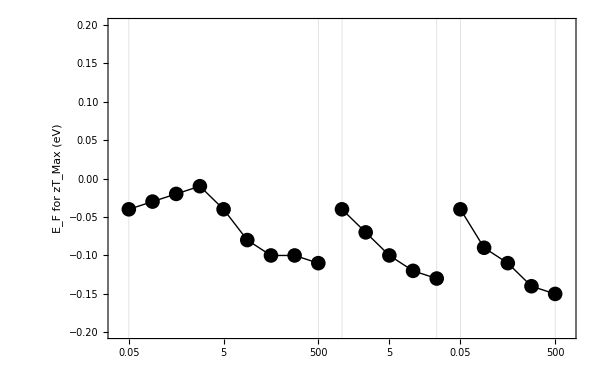
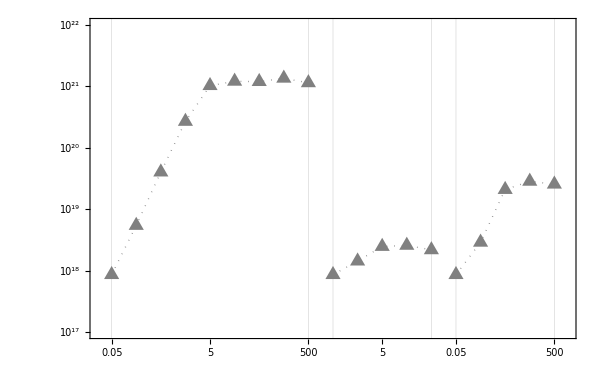

```mathematica
optimize="zt";

powerc=zetac^2/sigmac;
powerdefc=zetadefc^2/sigmadefc;
powerpolc=zetapolc^2/sigmapolc;
poweriic=zetaiic^2/sigmaiic;

ztc=powerc*T/(kappac+kappalat);
ztdefc=powerdefc*T/(kappadefc+kappalat);
ztpolc=powerpolc*T/(kappapolc+kappalat);
ztiic=poweriic*T/(kappaiic+kappalat);

index=ConstantArray[0,Nm];
If[optimize=="zt"||optimize=="zT"||optimize=="ZT",
Do[index⟦i⟧=Position[ztc⟦i,All⟧,Max[ztc⟦i,All⟧]]⟦1,1⟧,{i,Nm}]
]
If[optimize=="pf"||optimize=="PF",
Do[index⟦i⟧=Position[powerc⟦i,All⟧,Max[powerc⟦i,All⟧]]⟦1,1⟧,{i,Nm}]
]

mticks=Map[{#⟦1⟧,Rotate[#⟦2⟧,π/4]}&,{{1,0.05},{3,0.5},{5,5},{7,50},{9,500},{10,0.05},{12,5},{14,500},{15,0.05},{17,5},{19,500}}];

fermilevelplot=ListPlot[{Ef⟦index⟦Range[9]⟧⟧*h2ev,Table[{i,Ef⟦index⟦i⟧⟧*h2ev},{i,10,14}],Table[{i,Ef⟦index⟦i⟧⟧*h2ev},{i,15,19}]},PlotStyle->{{Black,Thick}},Frame->True,FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Gray,Dotted,25}},FrameTicks->{{Automatic,None},{mticks,None}},FrameLabel->{None,"E_F for zT_Max (eV)",None,None},Joined->True,PlotRange->{{0.5,Nm+0.5},{-0.2,0.2}},PlotMarkers->{{●,15}},GridLines->{{1,9,10,14,15,19},None},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->600,ImagePadding->100];
carrierplot=ListLogPlot[{Table[{i,populationc⟦i,index⟦i⟧⟧/(bohr2m^3*10^6)},{i,1,9}],Table[{i,populationc⟦i,index⟦i⟧⟧/(bohr2m^3*10^6)},{i,10,14}],Table[{i,populationc⟦i,index⟦i⟧⟧/(bohr2m^3*10^6)},{i,15,19}]},PlotStyle->{{Gray,Dotted,Thick}},Frame->True,FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Gray,Dotted,25}},FrameTicks->{{None,All},{mticks,None}},FrameLabel->{{None,"n for zT_Max (cm^-3)"},{None,None}},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^17,10^22}},PlotMarkers->{{▲,18}},GridLines->{{1,9,10,14,15,19},None},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->600,ImagePadding->100];

Overlay[{fermilevelplot,carrierplot}]
```

### Conductivity

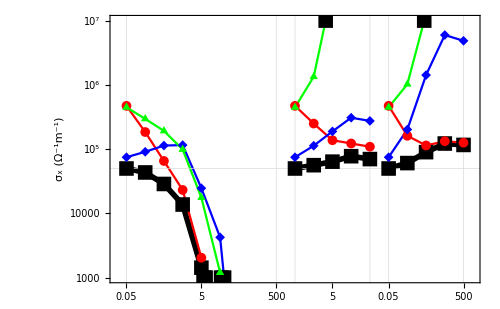

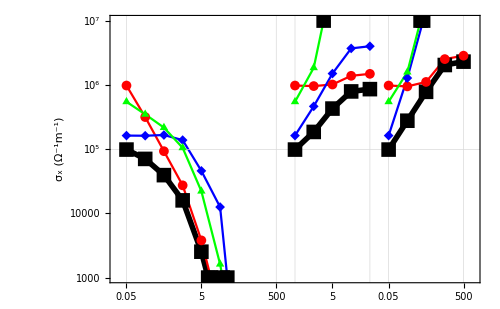

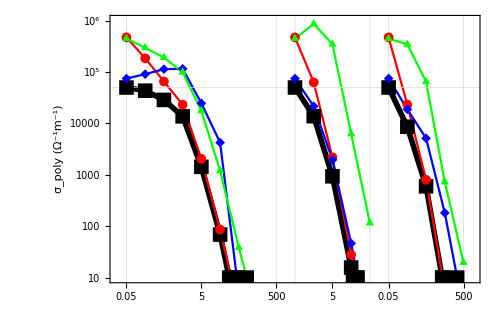

```mathematica
dir=1;

sigmac=sigmac*au2cond;sigmadefc=sigmadefc*au2cond;sigmapolc=sigmapolc*au2cond;sigmaiic=sigmaiic*au2cond;
sigmacpoly=sigmacpoly*au2cond;sigmadefcpoly=sigmadefcpoly*au2cond;sigmapolcpoly=sigmapolcpoly*au2cond;sigmaiicpoly=sigmaiicpoly*au2cond;
ListLogPlot[{Table[{i,sigmac⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,sigmadefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,sigmapolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,sigmaiic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,sigmac⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,sigmadefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,sigmapolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,sigmaiic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,sigmac⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,sigmadefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,sigmapolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,sigmaiic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"σ_x (Ω^-1m^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^3,10^7}},GridLines->{{1,9,10,14,15,19},{sigmac⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,sigmac⟦i,ef0,dir⟧},{i,1,9}],Table[{i,sigmadefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,sigmapolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,sigmaiic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,sigmac⟦i,ef0,dir⟧},{i,10,14}],Table[{i,sigmadefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,sigmapolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,sigmaiic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,sigmac⟦i,ef0,dir⟧},{i,15,19}],Table[{i,sigmadefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,sigmapolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,sigmaiic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"σ_x (Ω^-1m^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^3,10^7}},GridLines->{{1,9,10,14,15,19},{sigmac⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,sigmacpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmadefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmapolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmaiicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,sigmacpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmadefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmapolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmaiicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,sigmacpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,sigmadefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,sigmapolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,sigmaiicpoly⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"σ_poly (Ω^-1m^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^1,10^6}},GridLines->{{1,9,10,14,15,19},{sigmacpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
sigmac=sigmac/au2cond;sigmadefc=sigmadefc/au2cond;sigmapolc=sigmapolc/au2cond;sigmaiic=sigmaiic/au2cond;
sigmacpoly=sigmacpoly/au2cond;sigmadefcpoly=sigmadefcpoly/au2cond;sigmapolcpoly=sigmapolcpoly/au2cond;sigmaiicpoly=sigmaiicpoly/au2cond;
```

### Mobility

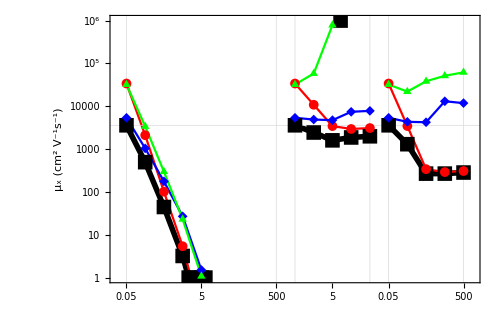

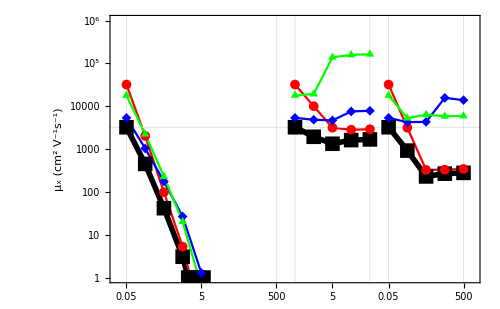

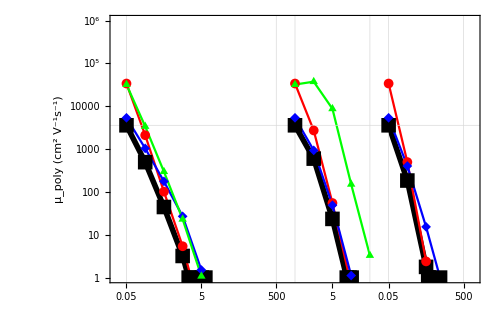

```mathematica
dir=1;

mobdefc=sigmadefc*au2cond/populationc*bohr2m^3/q*10^4;mobpolc=sigmapolc*au2cond/populationc*bohr2m^3/q*10^4;mobiic=sigmaiic*au2cond/populationc*bohr2m^3/q*10^4;
mobc=sigmac*au2cond/populationc*bohr2m^3/q*10^4;
mobdefcpoly=sigmadefcpoly*au2cond/populationc*bohr2m^3/q*10^4;mobpolcpoly=sigmapolcpoly*au2cond/populationc*bohr2m^3/q*10^4;mobiicpoly=sigmaiicpoly*au2cond/populationc*bohr2m^3/q*10^4;
mobcpoly=sigmacpoly*au2cond/populationc*bohr2m^3/q*10^4;

ListLogPlot[{Table[{i,mobc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,mobdefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,mobpolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,mobiic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,mobc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,mobdefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,mobpolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,mobiic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,mobc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,mobdefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,mobpolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,mobiic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"μ_x (cm^2 V^-1s^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^0,10^6}},GridLines->{{1,9,10,14,15,19},{mobc⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,mobc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,mobdefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,mobpolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,mobiic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,mobc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,mobdefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,mobpolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,mobiic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,mobc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,mobdefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,mobpolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,mobiic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"μ_x (cm^2 V^-1s^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^0,10^6}},GridLines->{{1,9,10,14,15,19},{mobc⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,mobcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobdefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobpolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobiicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,mobcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobdefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobpolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobiicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,mobcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,mobdefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,mobpolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,mobiic⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Frame->True,FrameLabel->{None,"μ_poly (cm^2 V^-1s^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^0,10^6}},GridLines->{{1,9,10,14,15,19},{mobcpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
```

### Thermoelectricity

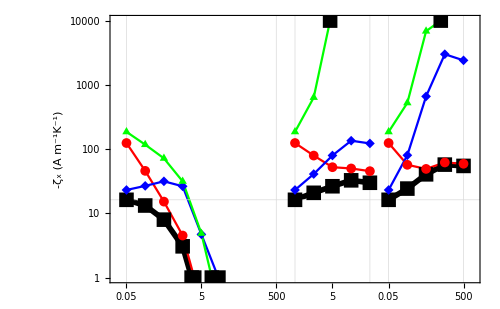

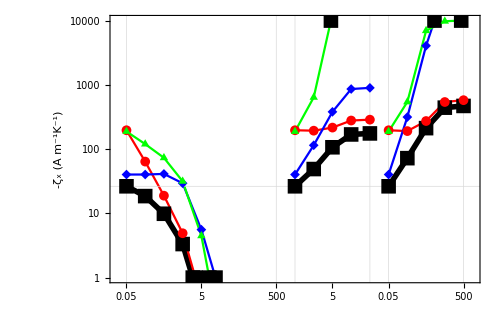

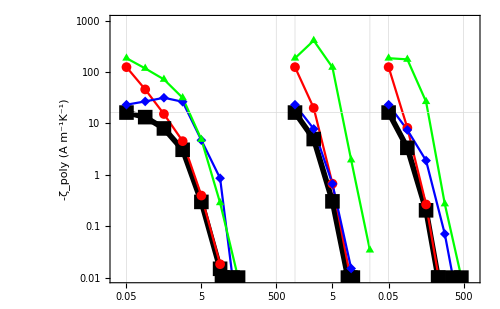

```mathematica
zetac=zetac*au2cond*h2ev*ev2j/q;zetadefc=zetadefc*au2cond*h2ev*ev2j/q;zetapolc=zetapolc*au2cond*h2ev*ev2j/q;zetaiic=zetaiic*au2cond*h2ev*ev2j/q;
zetacpoly=zetacpoly*au2cond*h2ev*ev2j/q;zetadefcpoly=zetadefcpoly*au2cond*h2ev*ev2j/q;zetapolcpoly=zetapolcpoly*au2cond*h2ev*ev2j/q;zetaiicpoly=zetaiicpoly*au2cond*h2ev*ev2j/q;

ListLogPlot[{Table[{i,-zetac⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-zetadefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-zetapolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-zetaiic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-zetac⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-zetadefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-zetapolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-zetaiic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-zetac⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,-zetadefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,-zetapolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,-zetaiic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-ζ_x (A m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^0,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-zetac⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,-zetac⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-zetadefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-zetapolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-zetaiic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-zetac⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-zetadefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-zetapolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-zetaiic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-zetac⟦i,ef0,dir⟧},{i,15,19}],Table[{i,-zetadefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,-zetapolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,-zetaiic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-ζ_x (A m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^0,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-zetac⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,-zetacpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetadefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetapolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetaiicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-zetacpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetadefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetapolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetaiicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-zetacpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-zetadefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-zetapolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-zetaiicpoly⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-ζ_poly (A m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-2,10^3}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-zetacpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

zetac=zetac/(au2cond*h2ev*ev2j/q);zetadefc=zetadefc/(au2cond*h2ev*ev2j/q);zetapolc=zetapolc/(au2cond*h2ev*ev2j/q);zetaiic=zetaiic/(au2cond*h2ev*ev2j/q);
zetacpoly=zetacpoly/(au2cond*h2ev*ev2j/q);zetadefcpoly=zetadefcpoly/(au2cond*h2ev*ev2j/q);zetapolcpoly=zetapolcpoly/(au2cond*h2ev*ev2j/q);zetaiicpoly=zetaiicpoly/(au2cond*h2ev*ev2j/q);
```

### Power Factor

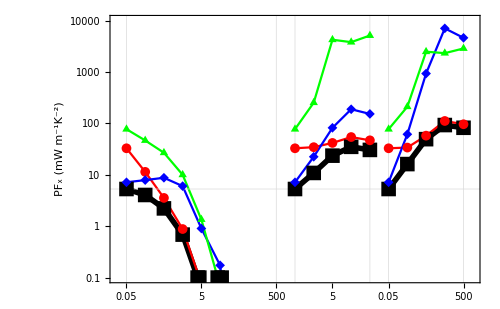

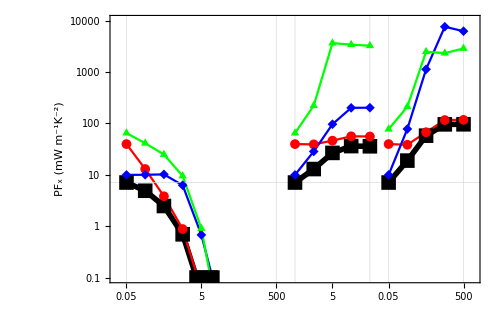

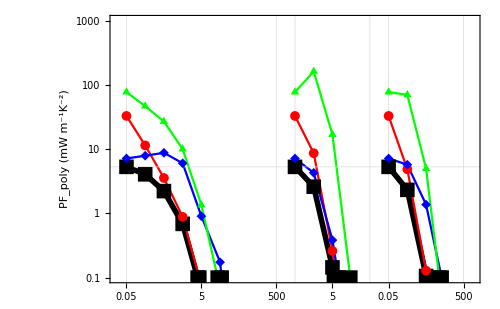

```mathematica
powerc=zetac^2/sigmac;
powerdefc=zetadefc^2/sigmadefc;
powerpolc=zetapolc^2/sigmapolc;
poweriic=zetaiic^2/sigmaiic;
powercpoly=zetacpoly^2/sigmacpoly;
powerdefcpoly=zetadefcpoly^2/sigmadefcpoly;
powerpolcpoly=zetapolcpoly^2/sigmapolcpoly;
poweriicpoly=zetaiicpoly^2/sigmaiicpoly;

dir =1;
powerc=powerc*au2cond*(h2ev*ev2j/q)^2*10^3;powerdefc=powerdefc*au2cond*(h2ev*ev2j/q)^2*10^3;powerpolc=powerpolc*au2cond*(h2ev*ev2j/q)^2*10^3;poweriic=poweriic*au2cond*(h2ev*ev2j/q)^2*10^3;
powercpoly=powercpoly*au2cond*(h2ev*ev2j/q)^2*10^3;powerdefcpoly=powerdefcpoly*au2cond*(h2ev*ev2j/q)^2*10^3;powerpolcpoly=powerpolcpoly*au2cond*(h2ev*ev2j/q)^2*10^3;poweriicpoly=poweriicpoly*au2cond*(h2ev*ev2j/q)^2*10^3;

ListLogPlot[{Table[{i,powerc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,powerdefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,powerpolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,poweriic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i+9,powerc⟦9+i,index⟦i⟧,dir⟧},{i,1,5}],Table[{i+9,powerdefc⟦9+i,index⟦i⟧,dir⟧},{i,1,5}],Table[{i+9,powerpolc⟦9+i,index⟦i⟧,dir⟧},{i,1,5}],Table[{i+9,poweriic⟦9+i,index⟦i⟧,dir⟧},{i,1,5}],Table[{i+14,powerc⟦14+i,index⟦i⟧,dir⟧},{i,1,5}],Table[{i+14,powerdefc⟦14+i,index⟦i⟧,dir⟧},{i,1,5}],Table[{i+14,powerpolc⟦14+i,index⟦i⟧,dir⟧},{i,1,5}],Table[{i+14,poweriic⟦14+i,index⟦i⟧,dir⟧},{i,1,5}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"PF_x (mW m^-1K^-2)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-1,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{powerc⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,powerc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,powerdefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,powerpolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,poweriic⟦i,ef0,dir⟧},{i,1,9}],Table[{i+9,powerc⟦9+i,ef0,dir⟧},{i,1,5}],Table[{i+9,powerdefc⟦9+i,ef0,dir⟧},{i,1,5}],Table[{i+9,powerpolc⟦9+i,ef0,dir⟧},{i,1,5}],Table[{i+9,poweriic⟦9+i,ef0,dir⟧},{i,1,5}],Table[{i+14,powerc⟦14+i,ef0,dir⟧},{i,1,5}],Table[{i+14,powerdefc⟦14+i,ef0,dir⟧},{i,1,5}],Table[{i+14,powerpolc⟦14+i,ef0,dir⟧},{i,1,5}],Table[{i+14,poweriic⟦14+i,index⟦i⟧,dir⟧},{i,1,5}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"PF_x (mW m^-1K^-2)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-1,10^4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{powerc⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,powercpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,powerdefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,powerpolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,poweriicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i+9,powercpoly⟦9+i,index⟦i⟧⟧},{i,1,5}],Table[{i+9,powerdefcpoly⟦9+i,index⟦i⟧⟧},{i,1,5}],Table[{i+9,powerpolcpoly⟦9+i,index⟦i⟧⟧},{i,1,5}],Table[{i+9,poweriicpoly⟦9+i,index⟦i⟧⟧},{i,1,5}],Table[{i+14,powercpoly⟦14+i,index⟦i⟧⟧},{i,1,5}],Table[{i+14,powerdefcpoly⟦14+i,index⟦i⟧⟧},{i,1,5}],Table[{i+14,powerpolcpoly⟦14+i,index⟦i⟧⟧},{i,1,5}],Table[{i+14,poweriicpoly⟦14+i,index⟦i⟧⟧},{i,1,5}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"PF_poly (mW m^-1K^-2)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-1,10^3}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{powercpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

powerdefc=powerdefc/(au2cond*(h2ev*ev2j/q)^2*10^3);
powerpolc=powerpolc/(au2cond*(h2ev*ev2j/q)^2*10^3);
poweriic=poweriic/(au2cond*(h2ev*ev2j/q)^2*10^3);
powerc=powerc/(au2cond*(h2ev*ev2j/q)^2*10^3);
powerdefcpoly=powerdefcpoly/(au2cond*(h2ev*ev2j/q)^2*10^3);
powerpolcpoly=powerpolcpoly/(au2cond*(h2ev*ev2j/q)^2*10^3);poweriicpoly=poweriicpoly/(au2cond*(h2ev*ev2j/q)^2*10^3);
powercpoly=powercpoly/(au2cond*(h2ev*ev2j/q)^2*10^3);
```

### Seebeck Coefficient

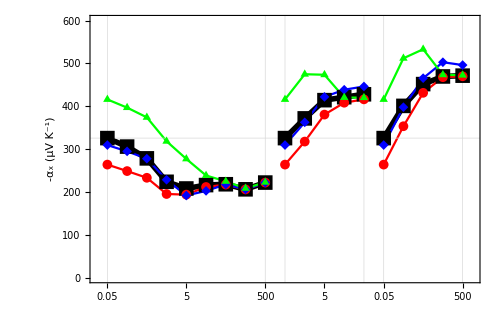

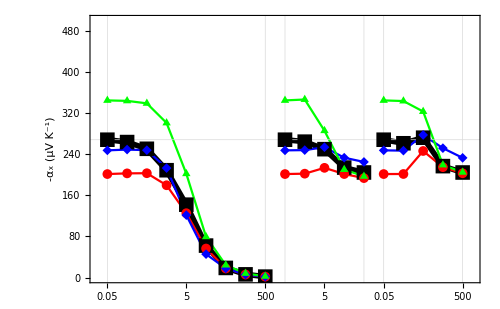

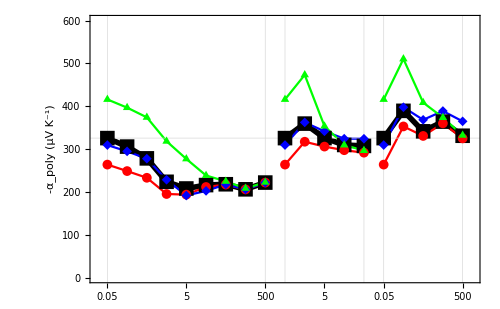

```mathematica
alphac=zetac/sigmac;
alphadefc=zetadefc/sigmadefc;
alphapolc=zetapolc/sigmapolc;
alphaiic=zetaiic/sigmaiic;
alphacpoly=zetacpoly/sigmacpoly;
alphadefcpoly=zetadefcpoly/sigmadefcpoly;
alphapolcpoly=zetapolcpoly/sigmapolcpoly;
alphaiicpoly=zetaiicpoly/sigmaiicpoly;

dir=1;

alphac=alphac*h2ev*ev2j/q*10^6;alphadefc=alphadefc*h2ev*ev2j/q*10^6;alphapolc=alphapolc*h2ev*ev2j/q*10^6;alphaiic=alphaiic*h2ev*ev2j/q*10^6;
alphacpoly=alphacpoly*h2ev*ev2j/q*10^6;alphadefcpoly=alphadefcpoly*h2ev*ev2j/q*10^6;alphapolcpoly=alphapolcpoly*h2ev*ev2j/q*10^6;alphaiicpoly=alphaiicpoly*h2ev*ev2j/q*10^6;

ListPlot[{Table[{i,-alphac⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-alphadefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-alphapolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-alphaiic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,-alphac⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-alphadefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-alphapolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-alphaiic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,-alphac⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,-alphadefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,-alphapolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,-alphaiic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-α_x (μV K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,600}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-alphac⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListPlot[{Table[{i,-alphac⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-alphadefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-alphapolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-alphaiic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,-alphac⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-alphadefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-alphapolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-alphaiic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,-alphac⟦i,ef0,dir⟧},{i,15,19}],Table[{i,-alphadefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,-alphapolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,-alphaiic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-α_x (μV K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,500}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-alphac⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListPlot[{Table[{i,-alphacpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphadefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphapolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphaiicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,-alphacpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphadefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphapolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphaiicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,-alphacpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-alphadefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-alphapolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,-alphaiicpoly⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"-α_poly (μV K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,600}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{-alphacpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

alphac=alphac/(h2ev*ev2j/q*10^6);alphadefc=alphadefc/(h2ev*ev2j/q*10^6);alphapolc=alphapolc/(h2ev*ev2j/q*10^6);alphaiic=alphaiic/(h2ev*ev2j/q*10^6);
alphacpoly=alphacpoly/(h2ev*ev2j/q*10^6);alphadefcpoly=alphadefcpoly/(h2ev*ev2j/q*10^6);alphapolcpoly=alphapolcpoly/(h2ev*ev2j/q*10^6);alphaiicpoly=alphaiicpoly/(h2ev*ev2j/q*10^6);
```

### Carrier Thermal Conductivity

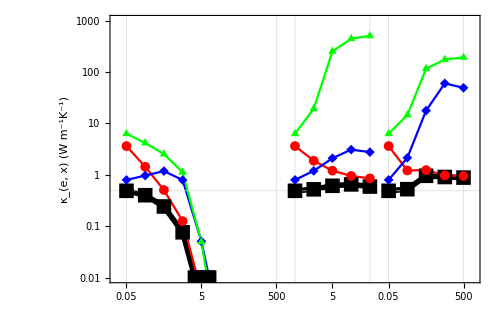

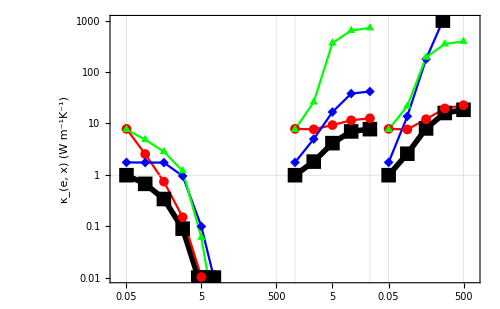

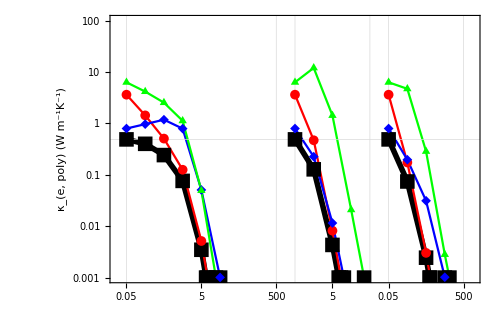

```mathematica
kappac=kappac*h2ev*ev2j/bohr2m/au2sec;kappadefc=kappadefc*h2ev*ev2j/bohr2m/au2sec;kappapolc=kappapolc*h2ev*ev2j/bohr2m/au2sec;kappaiic=kappaiic*h2ev*ev2j/bohr2m/au2sec;
kappacpoly=kappacpoly*h2ev*ev2j/bohr2m/au2sec;kappadefcpoly=kappadefcpoly*h2ev*ev2j/bohr2m/au2sec;kappapolcpoly=kappapolcpoly*h2ev*ev2j/bohr2m/au2sec;kappaiicpoly=kappaiicpoly*h2ev*ev2j/bohr2m/au2sec;

ListLogPlot[{Table[{i,kappac⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,kappadefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,kappapolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,kappaiic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,kappac⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,kappadefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,kappapolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,kappaiic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,kappac⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,kappadefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,kappapolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,kappaiic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"κ_(e,  x) (W m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-2,10^3}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{kappac⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,kappac⟦i,ef0,dir⟧},{i,1,9}],Table[{i,kappadefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,kappapolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,kappaiic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,kappac⟦i,ef0,dir⟧},{i,10,14}],Table[{i,kappadefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,kappapolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,kappaiic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,kappac⟦i,ef0,dir⟧},{i,15,19}],Table[{i,kappadefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,kappapolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,kappaiic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"κ_(e,  x) (W m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-2,10^3}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{kappac⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListLogPlot[{Table[{i,kappacpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappadefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappapolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappaiicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,kappacpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappadefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappapolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappaiicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,kappacpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,kappadefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,kappapolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,kappaiicpoly⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-5,10}],None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"κ_(e,  poly) (W m^-1K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{10^-3,10^2}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{kappacpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

kappac=kappac/(h2ev*ev2j/bohr2m/au2sec);kappadefc=kappadefc/(h2ev*ev2j/bohr2m/au2sec);kappapolc=kappapolc/(h2ev*ev2j/bohr2m/au2sec);kappaiic=kappaiic/(h2ev*ev2j/bohr2m/au2sec);
kappacpoly=kappacpoly/(h2ev*ev2j/bohr2m/au2sec);kappadefcpoly=kappadefcpoly/(h2ev*ev2j/bohr2m/au2sec);kappapolcpoly=kappapolcpoly/(h2ev*ev2j/bohr2m/au2sec);kappaiicpoly=kappaiicpoly/(h2ev*ev2j/bohr2m/au2sec);
```

### Lorenz Number

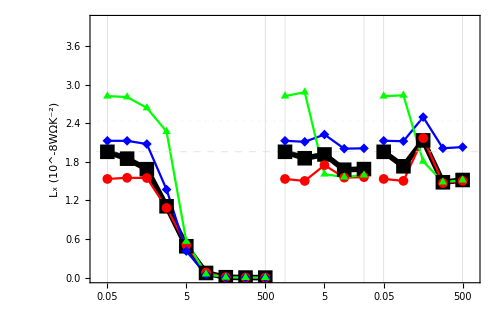

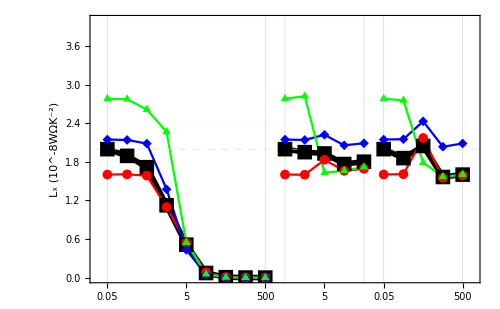

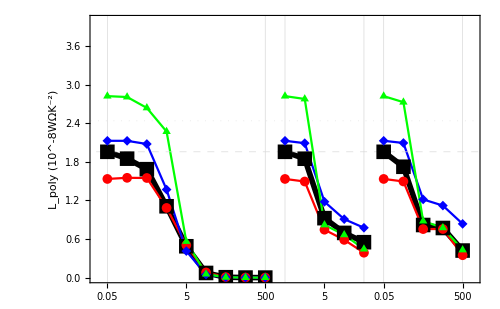

```mathematica
lorenzc=kappac/sigmac/T;
lorenzdefc=kappadefc/sigmadefc/T;
lorenzpolc=kappapolc/sigmapolc/T;
lorenziic=kappaiic/sigmaiic/T;
lorenzcpoly=kappacpoly/sigmacpoly/T;
lorenzdefcpoly=kappadefcpoly/sigmadefcpoly/T;
lorenzpolcpoly=kappapolcpoly/sigmapolcpoly/T;
lorenziicpoly=kappaiicpoly/sigmaiicpoly/T;

dir=1;
lorenzc=lorenzc*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;lorenzdefc=lorenzdefc*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
lorenzpolc=lorenzpolc*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
lorenziic=lorenziic*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
lorenzcpoly=lorenzcpoly*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;lorenzdefcpoly=lorenzdefcpoly*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
lorenzpolcpoly=lorenzpolcpoly*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;
lorenziicpoly=lorenziicpoly*h2ev*ev2j/bohr2m/au2sec/au2cond*10^8;

ListPlot[{Table[{i,lorenzc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,lorenzdefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,lorenzpolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,lorenziic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,lorenzc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,lorenzdefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,lorenzpolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,lorenziic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,lorenzc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,lorenzdefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,lorenzpolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,lorenziic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},FrameLabel->{None,"L_x (10^-8WΩK^-2)"},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Joined->True,PlotRange->{{0.5,Nm+0.5},{(*0.00001*)0,4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{{2.44,Dotted},{lorenzc⟦1,index⟦1⟧,dir⟧,Dashed}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black}},ImageSize->500]

ListPlot[{Table[{i,lorenzc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,lorenzdefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,lorenzpolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,lorenziic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,lorenzc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,lorenzdefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,lorenzpolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,lorenziic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,lorenzc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,lorenzdefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,lorenzpolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,lorenziic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},FrameLabel->{None,"L_x (10^-8WΩK^-2)"},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Joined->True,PlotRange->{{0.5,Nm+0.5},{(*0.00001*)0,4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{{2.44,Dotted},{lorenzc⟦1,ef0,dir⟧,Dashed}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black}},ImageSize->500]

ListPlot[{Table[{i,lorenzcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenzdefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenzpolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenziicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,lorenzcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenzdefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenzpolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenziicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,lorenzcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,lorenzdefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,lorenzpolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,lorenziicpoly⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},FrameLabel->{None,"L_poly (10^-8WΩK^-2)"},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},Joined->True,PlotRange->{{0.5,Nm+0.5},{(*0.00001*)0,4}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{{2.44,Dotted},{lorenzcpoly⟦1,index⟦1⟧⟧,Dashed}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black}},ImageSize->500]

lorenzc=lorenzc/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);lorenzdefc=lorenzdefc/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
lorenzpolc=lorenzpolc/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
lorenziic=lorenziic/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
lorenzcpoly=lorenzcpoly/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);lorenzdefcpoly=lorenzdefcpoly/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
lorenzpolcpoly=lorenzpolcpoly/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
lorenziicpoly=lorenziicpoly/(h2ev*ev2j/bohr2m/au2sec/au2cond*10^8);
```

### ZT

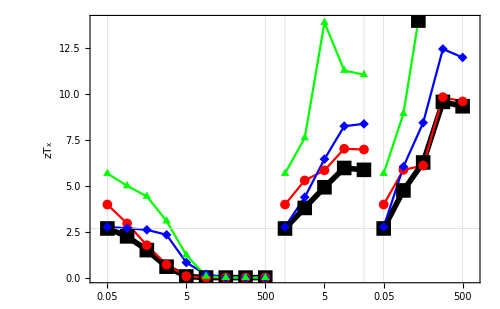

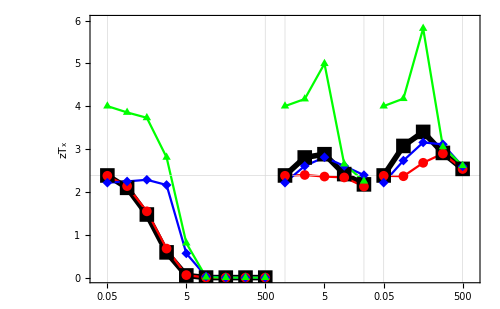

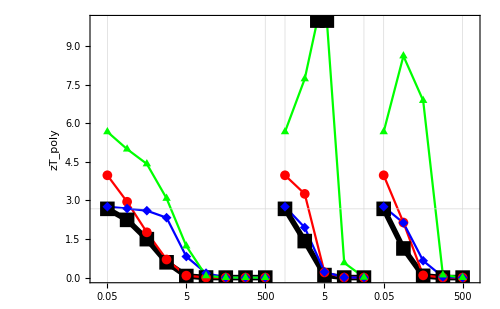

```mathematica
ztc=powerc*T/(kappac+kappalat);
ztdefc=powerdefc*T/(kappadefc+kappalat);
ztpolc=powerpolc*T/(kappapolc+kappalat);
ztiic=poweriic*T/(kappaiic+kappalat);
ztcpoly=powercpoly*T/(kappacpoly+kappalat);
ztdefcpoly=powerdefcpoly*T/(kappadefcpoly+kappalat);
ztpolcpoly=powerpolcpoly*T/(kappapolcpoly+kappalat);
ztiicpoly=poweriicpoly*T/(kappaiicpoly+kappalat);

dir=1;

ListPlot[{Table[{i,ztc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,ztdefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,ztpolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,ztiic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,ztc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,ztdefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,ztpolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,ztiic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,ztc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,ztdefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,ztpolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,ztiic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"zT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,14}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztc⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListPlot[{Table[{i,ztc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,ztdefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,ztpolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,ztiic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,ztc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,ztdefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,ztpolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,ztiic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,ztc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,ztdefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,ztpolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,ztiic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"zT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,6}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztc⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListPlot[{Table[{i,ztcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztdefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztpolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztiicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztdefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztpolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztiicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztdefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztpolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztiicpoly⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thickness[0.008]},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"zT_poly"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,10}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztcpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
```

### Electronic-part zT

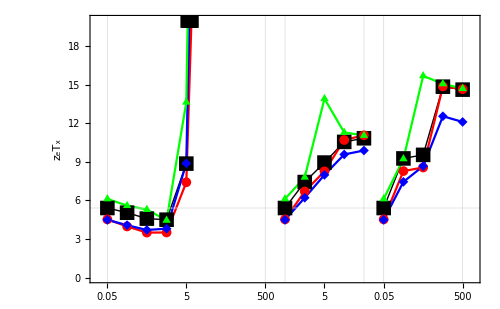

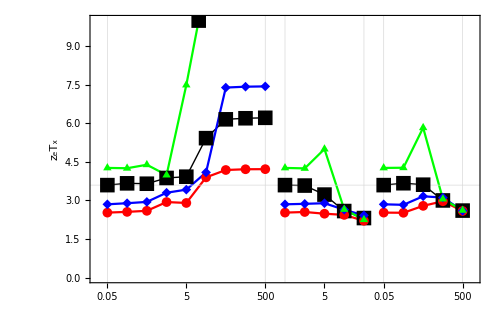

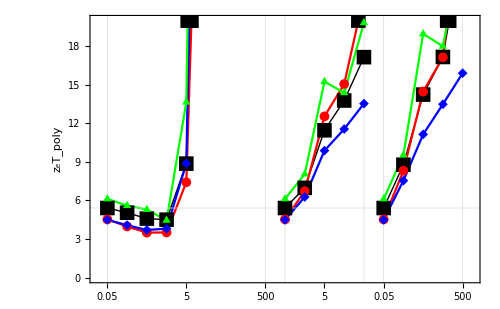

```mathematica
ztec=powerc*T/(kappac);
ztedefc=powerdefc*T/(kappadefc);
ztepolc=powerpolc*T/(kappapolc);
zteiic=poweriic*T/(kappaiic);
ztecpoly=powercpoly*T/(kappacpoly);
ztedefcpoly=powerdefcpoly*T/(kappadefcpoly);
ztepolcpoly=powerpolcpoly*T/(kappapolcpoly);
zteiicpoly=poweriicpoly*T/(kappaiicpoly);

dir=1;

ListPlot[{Table[{i,ztec⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,ztedefc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,ztepolc⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,zteiic⟦i,index⟦i⟧,dir⟧},{i,1,9}],Table[{i,ztec⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,ztedefc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,ztepolc⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,zteiic⟦i,index⟦i⟧,dir⟧},{i,10,14}],Table[{i,ztec⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,ztedefc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,ztepolc⟦i,index⟦i⟧,dir⟧},{i,15,19}],Table[{i,zteiic⟦i,index⟦i⟧,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thick},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"z_eT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,20}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztec⟦1,index⟦1⟧,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListPlot[{Table[{i,ztec⟦i,ef0,dir⟧},{i,1,9}],Table[{i,ztedefc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,ztepolc⟦i,ef0,dir⟧},{i,1,9}],Table[{i,zteiic⟦i,ef0,dir⟧},{i,1,9}],Table[{i,ztec⟦i,ef0,dir⟧},{i,10,14}],Table[{i,ztedefc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,ztepolc⟦i,ef0,dir⟧},{i,10,14}],Table[{i,zteiic⟦i,ef0,dir⟧},{i,10,14}],Table[{i,ztec⟦i,ef0,dir⟧},{i,15,19}],Table[{i,ztedefc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,ztepolc⟦i,ef0,dir⟧},{i,15,19}],Table[{i,zteiic⟦i,ef0,dir⟧},{i,15,19}]},PlotStyle->{{Black,Thick},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"z_eT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,10}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztec⟦1,ef0,dir⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]

ListPlot[{Table[{i,ztecpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztedefcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztepolcpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,zteiicpoly⟦i,index⟦i⟧⟧},{i,1,9}],Table[{i,ztecpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztedefcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztepolcpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,zteiicpoly⟦i,index⟦i⟧⟧},{i,10,14}],Table[{i,ztecpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztedefcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,ztepolcpoly⟦i,index⟦i⟧⟧},{i,15,19}],Table[{i,zteiicpoly⟦i,index⟦i⟧⟧},{i,15,19}]},PlotStyle->{{Black,Thick},{Red},{Blue},{Green}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"z_eT_poly"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,20}},PlotMarkers->{{■,15},{●,10},{◆,10},{▲,10}},GridLines->{{1,9,10,14,15,19},{ztecpoly⟦1,index⟦1⟧⟧}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
```

### METALLIC (gap=0, E_F=0)

```mathematica
fix=1;dir=1;
sigma=ConstantArray[0,Nm];zeta=ConstantArray[0,Nm];kappa=ConstantArray[0,Nm];
Do[
sigma⟦m⟧=sigmadefc⟦fix,ef0,dir⟧+sigmadefc⟦m,ef0,dir⟧;
zeta⟦m⟧=zetadefc⟦fix,ef0,dir⟧-zetadefc⟦m,ef0,dir⟧;
kappa⟦m⟧=kappadefc⟦fix,ef0,dir⟧+kappadefc⟦m,ef0,dir⟧;
,{m,Nm}]
alpha=zeta/sigma;
power=zeta^2/sigma;
L=kappa/sigma/T;

kappalat=0.5/(h2ev*ev2j/bohr2m/au2sec);
zT=power*T/(kappa+kappalat);
```

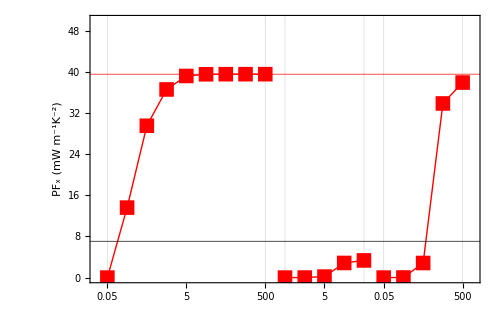

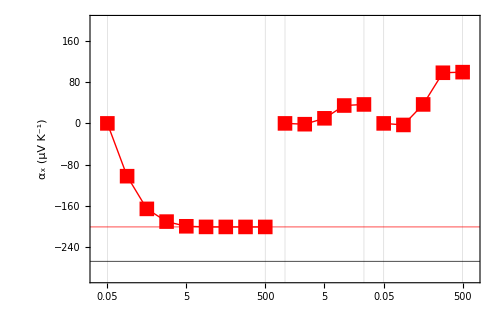

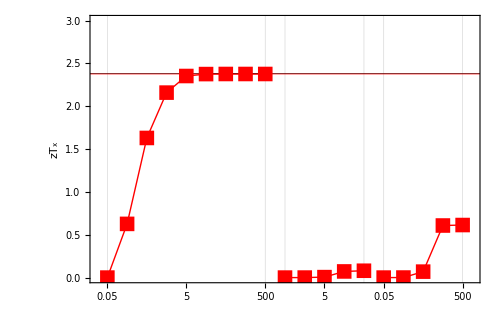

```mathematica
power=power*au2cond*(h2ev*ev2j/q)^2*10^3;
powerc=powerc*au2cond*(h2ev*ev2j/q)^2*10^3;
powerdefc=powerdefc*au2cond*(h2ev*ev2j/q)^2*10^3;
ListPlot[{power⟦Range[9]⟧,Table[{i+9,power⟦9+i⟧},{i,1,5}],Table[{i+14,power⟦14+i⟧},{i,1,5}]},PlotStyle->{{Red,Thick}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"PF_x (mW m^-1K^-2)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,50}},PlotMarkers->{{■,15}},GridLines->{{1,9,10,14,15,19},{{powerc⟦1,ef0,dir⟧,Black},{powerdefc⟦1,ef0,dir⟧,Red}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
power=power/(au2cond*(h2ev*ev2j/q)^2*10^3);
powerc=powerc/(au2cond*(h2ev*ev2j/q)^2*10^3);
powerdefc=powerdefc/(au2cond*(h2ev*ev2j/q)^2*10^3);

alpha=alpha*h2ev*ev2j/q*10^6;
alphac=alphac*h2ev*ev2j/q*10^6;
alphadefc=alphadefc*h2ev*ev2j/q*10^6;
ListPlot[{alpha⟦Range[9]⟧,Table[{i+9,alpha⟦9+i⟧},{i,1,5}],Table[{i+14,alpha⟦14+i⟧},{i,1,5}]},PlotStyle->{{Red,Thick}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"α_x (μV K^-1)"},Joined->True,PlotRange->{{0.5,Nm+0.5},{-300,200}},PlotMarkers->{{■,15}},GridLines->{{1,9,10,14,15,19},{{alphac⟦1,ef0,dir⟧,Black},{alphadefc⟦1,ef0,dir⟧,Red}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Black,Dashed}},ImageSize->500]
alpha=alpha/(h2ev*ev2j/q*10^6);
alphac=alphac/(h2ev*ev2j/q*10^6);
alphadefc=alphadefc/(h2ev*ev2j/q*10^6);

ListPlot[{zT⟦Range[9]⟧,Table[{i+9,zT⟦9+i⟧},{i,1,5}],Table[{i+14,zT⟦14+i⟧},{i,1,5}]},PlotStyle->{{Red,Thick}},Frame->True,FrameTicks->{{Automatic,None},{mticks,None}},FrameStyle->{{Thick,Black,20},{Thick,Black,25},{Thick,Black,25},{Thick,Black,25}},FrameLabel->{None,"zT_x"},Joined->True,PlotRange->{{0.5,Nm+0.5},{0,3}},PlotMarkers->{{■,15}},GridLines->{{1,9,10,14,15,19},{{ztc⟦1,ef0,dir⟧,Black},{ztdefc⟦1,ef0,dir⟧,Red}}},GridLinesStyle->{{Thickness[0.002],Gray},{Thickness[0.002],Dashed}},ImageSize->500]
```